# Mathematical Recreations: How fair is Monopoly? & Monopoly revisited

Monopoly básico : de la versión How fair is Monopoly?

(X_n) : Cadena de Markov, porque la probabilidad de caer en una casilla solo depende de la casilla actual desde donde lanzamos; Homogenea, porque la probabilidad no depende de n, el número de lanzamiento.
X_n : Variable aleatoria que indica la casilla donde estamos en el lanzamiento n.
α = (1, 0, ..., 0) : Distribución inicial de probabilidad, todos parten de la casilla inicial.

TODO: Añadir estudio teórico sobre ergódica y tal que asegura que existe la límite.

En la primera versión, la matriz de transición es la más simple, utilizando lanzamientos “fantasma” del dado para simular el lanzamiento de dos dados:

```mathematica
(* Matriz de transición de la Cadena de Markov *)
( M = Table[ If[  1 <= Mod[j-i, 40]  ≤ 6,1/6, 0] , {i,40},{j,40}] ) // MatrixForm
```

(0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6
1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6 | 1/6
1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6
1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 1/6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

También podemos trabajar directamente con M^2 que es la matriz de transición lanzando dos dados.

```mathematica
M2 = MatrixPower[M,2] ;
```

```mathematica
M2 [[1]]
```

{0,0,1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

La distribución inicial α

```mathematica
N[MatrixPower[M2,100],2] // MatrixForm ; (* Ver que es regular por el teorema *)
```

```mathematica
α=ConstantArray[0,40]; α[[1]] = 1; α
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Veamos numéricamente cómo la distribución inicial evoluciona.

```mathematica
α.M
```

{0,1/6,1/6,1/6,1/6,1/6,1/6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Manipulate[ListPlot[α.MatrixPower[M,y], PlotRange->{{0,40},{0,0.17}},Filling->Bottom], {y,1,100,1}]
```

ListPlot::lpn: α.MatrixPower[M,100.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[M,100.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.{{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,0.0249792,0.0249839,0.0249891,0.0249945,«21»,0.0249945,0.0249891,0.0249839,0.0249792,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M,100.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M,100.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {{0.02496456656818617,0.02496500281252998,0.02496630080377787,0.0249684285810776,0.02497133375149047,«31»,0.02497133375149047,0.0249684285810776,0.02496630080377787,0.02496500281252998},«38»,{«43»,«38»,«44»}} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,0.0249792,0.0249839,0.0249891,0.0249945,«21»,0.0249945,0.0249891,0.0249839,0.0249792,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,«29»,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,0.0249792,0.0249839,0.0249891,0.0249945,«21»,0.0249945,0.0249891,0.0249839,0.0249792,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} have incompatible shapes.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,«29»,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} is not a list of numbers or pairs of numbers.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,0.0249792,0.0249839,0.0249891,0.0249945,«21»,0.0249945,0.0249891,0.0249839,0.0249792,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0249646,0.024965,0.0249663,0.0249684,0.0249713,0.0249749,«29»,0.0249749,0.0249713,0.0249684,0.0249663,0.024965},«38»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M,100.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[ListPlot[α.MatrixPower[M2,y], PlotRange->{{0,40},{0,0.17}}, Filling->Bottom], {y,1,100,1}]
```

ListPlot::lpn: α.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: α.MatrixPower[M2,10.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Eigensystem[N[M],2]
```

{{1.,0.822277+0.503892 ⅈ},{{0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ,0.158114+0. ⅈ},{0.092937-0.127917 ⅈ,0.111803-0.111803 ⅈ,0.127917-0.092937 ⅈ,0.140881-0.0717822 ⅈ,0.150375-0.0488599 ⅈ,0.156167-0.0247345 ⅈ,0.158114+0. ⅈ,0.156167+0.0247345 ⅈ,0.150375+0.0488599 ⅈ,0.140881+0.0717822 ⅈ,0.127917+0.092937 ⅈ,0.111803+0.111803 ⅈ,0.092937+0.127917 ⅈ,0.0717822+0.140881 ⅈ,0.0488599+0.150375 ⅈ,0.0247345+0.156167 ⅈ,2.72988×10^-16+0.158114 ⅈ,-0.0247345+0.156167 ⅈ,-0.0488599+0.150375 ⅈ,-0.0717822+0.140881 ⅈ,-0.092937+0.127917 ⅈ,-0.111803+0.111803 ⅈ,-0.127917+0.092937 ⅈ,-0.140881+0.0717822 ⅈ,-0.150375+0.0488599 ⅈ,-0.156167+0.0247345 ⅈ,-0.158114-1.77389×10^-16 ⅈ,-0.156167-0.0247345 ⅈ,-0.150375-0.0488599 ⅈ,-0.140881-0.0717822 ⅈ,-0.127917-0.092937 ⅈ,-0.111803-0.111803 ⅈ,-0.092937-0.127917 ⅈ,-0.0717822-0.140881 ⅈ,-0.0488599-0.150375 ⅈ,-0.0247345-0.156167 ⅈ,-1.24403×10^-16-0.158114 ⅈ,0.0247345-0.156167 ⅈ,0.0488599-0.150375 ⅈ,0.0717822-0.140881 ⅈ}}}

```mathematica
Eigenvectors[N[M],1][[1]]/Total[Eigenvectors[N[M],1][[1]]]
```

{0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ,0.025+0. ⅈ}

```mathematica
0.8222767348221041+0.5038918311681153 ⅈ // Abs
```

0.964389

```mathematica
Eigensystem[M,1]
```

{{1},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Eigensystem[M2,1]
```

{{1},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}}

```mathematica
Eigenvectors[M,1][[1]]/Total[Eigenvectors[M,1][[1]]]
```

{1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40}

```mathematica
est=Eigenvectors[M,1][[1]]/Total[Eigenvectors[M,1][[1]]]
```

{1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40}

```mathematica
est.M
```

{1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40,1/40}

Monopoly básico : de la versión How fair is Monopoly?

------------------------

Empezamos modelizando la tirada de un dado múltiples veces en caso de sacar dobles, pero tres dobles seguidos llevan a la carcel.
X_n : Variable aleatoria que indica la casilla más lejana donde estamos en el lanzamiento n (la última tras repetir lanzamientos).

{0,0,1/36,1/18,1/12,1/9,5/36,1/6,5/36,1/9,1/12,1/18,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

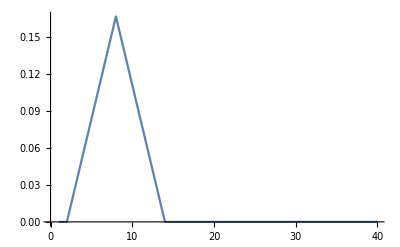

```mathematica
(* Tirada de un dado *)
M = Table[ If[  1 <= Mod[j-i, 40]  ≤ 6,1/6, 0] , {i,40},{j,40}] ;
(* Tirada de dos dados *)
M = MatrixPower[M,2]; 
dice =M[[1]]
ListPlot[dice, Joined->True]
```

```mathematica
(* Cómo se distribuye la probabilidad de sacar dobles tras la siguiente tirada *)
```

```mathematica
diceS1 = {0,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

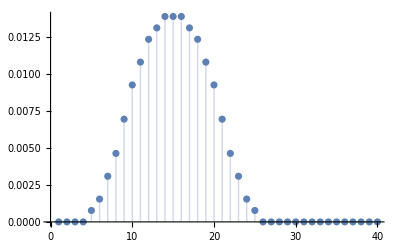

```mathematica
diceS1.M;
ListPlot[diceS1.M, Filling->Bottom]
```

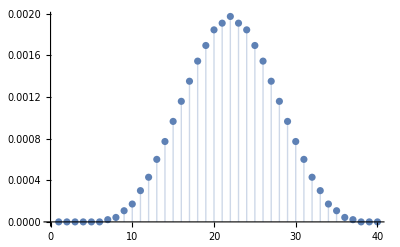

```mathematica
diceS2 = {0,0,0,0,1/1296,0,2/1296,0,3/1296,0,4/1296,0,5/1296,0,6/1296,0,5/1296,0,4/1296,0,3/1296,0,2/1296,0,1/1296,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
diceS2.M;
ListPlot[diceS2.M, Filling->Bottom]
```

```mathematica
diceS3 = {0,0,0,0,0,0,1/46656,0,3/46656,0,6/46656,0,(1+2+3+4)/46656,0,(5+4+3+2+1)/46656,0,(6+5+4+3+2+1)/46656,0,(5+6+5+4+3+2)/46656,0,(4+5+6+5+4+3)/46656,0,(3+4+5+6+5+4)/46656,0,(2+3+4+5+6+5)/46656,0,(1+2+3+4+5+6)/46656,0,(1+2+3+4+5)/46656,0,(1+2+3+4)/46656,0,6/46656,0,3/46656,0,1/46656,0,0,0};
Total[diceS3](* Debe ser 1/216, las probabilidad de 3 dobles seguidos, 6*6*6=216 *)
```

1/216

{0,0,0,1/18,1/18,73/648,73/648,3997/23328,2701/23328,703/5832,397/5832,797/11664,25/2592,19/1296,77/7776,13/864,79/7776,1/72,23/2592,259/23328,139/23328,77/11664,67/23328,79/23328,1/864,1/648,7/7776,1/864,5/7776,1/1296,1/2592,5/11664,1/5832,1/5832,1/23328,1/23328,0,0,0,0}

1

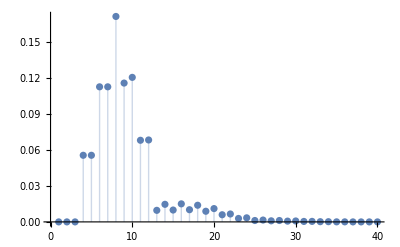

```mathematica
DICE = dice - diceS1 + diceS1.M -diceS2 + diceS2.M - diceS3; DICE[[10+1]]+=1/216;
(* El triple tiro de dobles : sacar diceS3 y darselo a la carcel *)
DICE
Total[DICE]
ListPlot[DICE, Filling->Bottom]
```

```mathematica
(* Matriz probabilidades de dobles del primer lanzamiento *)
diceS1;
( DICES1 = Table[  diceS1[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  )// MatrixForm;
(* Matriz probabilidades de dobles del primer lanzamiento distribuidas en el segundo lanzamiento *)
diceS1.M;
( DICES1M = Table[  (diceS1.M)[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  );
(* Matriz probabilidades de dobles del segundo lanzamiento *)
diceS2;
( DICES2 = Table[  diceS2[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  );  DICES2[[2]];
(* Matriz probabilidades de dobles del segundo lanzamiento distribuidas en el tercer lanzamiento *)
diceS2.M;
( DICES2M = Table[  (diceS2.M)[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  );
(* Matriz probabilidades de dobles del tercer lanzamiento *)
diceS3;
( DICES3 = Table[  diceS3[[Mod[j-i+1,40,1]]] , {i,40}, {j,40} ]  );
(* Matriz de transición : Tirar 2 dados
						- Prob. dobles
						+ Prob. distribuida en segundo lanzamiento
						- Prob. dobles en segundo lanzamiento
						+ Prob. distribuida en tercer lanzamiento
						- Prob. dobles en tercer lanzamiento
						# Añadir probabilidad dobles en tercer lanzamiento a la carcel
*)
( P = M - DICES1 + DICES1M  - DICES2 + DICES2M - DICES3 );
```

```mathematica
(* Aplica antes la regla de 3 dobles que las de ir a la carcel por la carta de suerte o casilla GO TO JAIL, y salir de la carcel antes que las de suerte *)
```

```mathematica
(* Añadimos las filas y columnas que corresponden a la estancia en la carcel *)
zeroes = ConstantArray[0,40];
( P=Transpose[Insert[Transpose[P],zeroes,41]] );
( P=Transpose[Insert[Transpose[P],zeroes,42]] );
zeroes = ConstantArray[0,42];
( P = Insert[P,zeroes, 41]);
( P = Insert[P,zeroes, 42]) //MatrixForm;
(* GO TO JAIL if 3 consecutive doubles or GOTOJAIL *)
For[i=1, i≤ 40,i++,
P[[i,41]] += 1/216 + P[[i,31]];
P[[i,31]] = 0; P[[31,i]] = 0;
]
P[[31,41]]=1;
(* KEEP ON JAIL or GET OUT OF JAIL if a double *)
outofJail =  {0,0,0,0,0,0,0,0,0,0,0,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,1/36,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
P[[41]] = outofJail; P[[42]] = outofJail;
(* No doubles *) 
P[[41, 42]] = 1-6/36; P[[42, 11]]=1-6/36; 

(* Chance card & Community chest: GO TO JAIL 1/16 *)
For[i=1, i≤ 40,i++,
P[[i,41]] += P[[i,8]] *(1/16);    P[[i,8]]  -=P[[i,8]] *(1/16);
P[[i,41]] += P[[i,18]] *(1/16);  P[[i,18]]-=P[[i,18]] *(1/16);
P[[i,41]] += P[[i,23]] *(1/16);  P[[i,23]]-= P[[i,23]] *(1/16);
P[[i,41]] += P[[i,34]] *(1/16);  P[[i,34]]-= P[[i,34]] *(1/16);
P[[i,41]] += P[[i,37]] *(1/16);  P[[i,37]]-=P[[i,37]] *(1/16);
]
```

```mathematica
P // MatrixForm
```

(0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 0 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 29/1728 | 0
0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 0 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 35/2592 | 0
0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 0 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 1699/124416 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 0 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 3959/373248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 0 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 3931/373248 | 0
1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 0 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1439/186624 | 0
1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 0 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 4027/373248 | 0
1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 0 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 2431/186624 | 0
1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 0 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 2947/186624 | 0
5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 0 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 7289/373248 | 0
1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 0 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1379/62208 | 0
1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 0 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1133/41472 | 0
5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 0 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 1555/62208 | 0
1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 0 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 11239/373248 | 0
7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 0 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 9847/373248 | 0
1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 0 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1951/62208 | 0
1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 0 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 8525/373248 | 0
79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 0 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 10333/373248 | 0
67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 0 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 25/1296 | 0
77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 0 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 14549/186624 | 0
139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 0 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 13007/186624 | 0
259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 0 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 47317/373248 | 0
23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 0 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 7801/62208 | 0
1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 0 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 11255/62208 | 0
79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 0 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 977/7776 | 0
13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 0 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 24071/186624 | 0
77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 0 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 28105/373248 | 0
19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 1039/13824 | 0
25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 815/41472 | 0
797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 7247/373248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 289/23328 | 0
2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 95/10368 | 0
3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 275/31104 | 0
73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 541/93312 | 0
73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 2063/373248 | 0
1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 0 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1171/124416 | 0
1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 0 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 383/41472 | 0
0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 0 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 4891/373248 | 0
0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 0 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 1219/93312 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
α=ConstantArray[0,42]; α[[1]] = 1; α
Manipulate[ListPlot[α.MatrixPower[P,y], PlotRange->{{0,43},{0,0.17}},Filling->Bottom], {y,1,500,1}]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.MatrixPower[P,500.] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,«6»,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«21»,«40»,«20»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,«13»,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,«6»,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«21»,«40»,«20»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,«13»,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,«6»,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«21»,«40»,«20»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,«13»,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,«6»,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«21»,«40»,«20»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,«13»,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Dot::dotsh: Tensors {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0} and {«1»} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.} and {{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,«6»,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«21»,«40»,«20»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

ListPlot::lpn: {1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}.{{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,«13»,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731},«40»,{«1»}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
For[i=1, i≤ 42,i++, If[Total[P[[i]]]≠1, Print["Error en fila ", i, " : ", Total[P[[i]]]]] ]
```

```mathematica
Eigensystem[P,2]
```

```mathematica
Eigensystem[N[P],2]
```

{{1.,0.251911+0.781808 ⅈ},{{0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ,0.154303+0. ⅈ},{-0.0447697+0.143968 ⅈ,-0.0683961+0.135025 ⅈ,-0.0889812+0.12218 ⅈ,-0.108286+0.106401 ⅈ,-0.123613+0.0873896 ⅈ,-0.137115+0.0664351 ⅈ,-0.144856+0.0434064 ⅈ,-0.150943+0.0193072 ⅈ,-0.151354-0.00525753 ⅈ,-0.149962-0.0290818 ⅈ,-0.142327-0.0524807 ⅈ,-0.132995-0.0733254 ⅈ,-0.118181-0.0940439 ⅈ,-0.10168-0.110889 ⅈ,-0.0809189-0.127235 ⅈ,-0.0600563-0.138787 ⅈ,-0.0376307-0.149997 ⅈ,-0.0158602-0.155295 ⅈ,0.00592897-0.159288 ⅈ,0.0318131-0.14868 ⅈ,0.0523279-0.145046 ⅈ,0.0768398-0.127195 ⅈ,0.0965415-0.11546 ⅈ,0.119185-0.0912437 ⅈ,0.130805-0.0819305 ⅈ,0.144286-0.0612296 ⅈ,0.150195-0.0473093 ⅈ,0.157062-0.0237271 ⅈ,0.155397-0.00777815 ⅈ,0.154301+0.0166083 ⅈ,0.188656+0. ⅈ,0.140479+0.0636835 ⅈ,0.128171+0.0852375 ⅈ,0.112423+0.104428 ⅈ,0.0940273+0.121154 ⅈ,0.07303+0.134527 ⅈ,0.0511558+0.144023 ⅈ,0.0269819+0.150114 ⅈ,0.00317796+0.15194 ⅈ,-0.0216613+0.150087 ⅈ,0.0475245+0.147493 ⅈ,-0.121276+0.115541 ⅈ}}}

```mathematica
est = Re[Eigenvectors[N[P],1][[1]]/Total[Eigenvectors[N[P],1][[1]]] ]
```

{0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095}

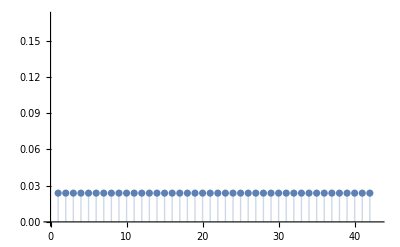

```mathematica
ListPlot[est, PlotRange->{{0,43},{0,0.17}},Filling->Bottom]
```

```mathematica
0.25191099048468757+0.7818075114838076 ⅈ // Abs
```

0.82139

```mathematica
est
est.P
MatrixPower[N[P],100000] // MatrixForm
```

{0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095,0.0238095}

{0.0221887,0.0220724,0.0234697,0.0233502,0.0234635,0.023341,0.0234574,0.0219081,0.023488,0.0234349,0.0433987,0.0235421,0.0249537,0.0236187,0.0249945,0.0236626,0.0250006,0.0221923,0.0250067,0.0236809,0.0250129,0.0236891,0.023537,0.0236952,0.0236983,0.0236983,0.0236993,0.0236993,0.0236993,0.0236993,0.,0.0236993,0.0236993,0.020978,0.0223765,0.021017,0.0197035,0.0196198,0.0209425,0.0208293,0.0589408,0.0198413}

(0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731
0.0218519 | 0.0213578 | 0.0222406 | 0.021798 | 0.0215178 | 0.0214029 | 0.0213821 | 0.0200293 | 0.0214609 | 0.0215034 | 0.0468384 | 0.0214143 | 0.0231683 | 0.0226745 | 0.0244286 | 0.0241601 | 0.0260766 | 0.0244182 | 0.0267124 | 0.0255818 | 0.0262831 | 0.0252228 | 0.0243843 | 0.0248014 | 0.0247831 | 0.0253216 | 0.0251306 | 0.0253764 | 0.0250661 | 0.0251504 | 0. | 0.0249845 | 0.0249213 | 0.0221163 | 0.0236038 | 0.0221934 | 0.0206452 | 0.0204494 | 0.0214863 | 0.0210212 | 0.0365677 | 0.0304731)

```mathematica
est = MatrixPower[N[P],100000][[1]]
```

{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,0.0267124,0.0255818,0.0262831,0.0252228,0.0243843,0.0248014,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731}

```mathematica
est.P
```

{0.0218519,0.0213578,0.0222406,0.021798,0.0215178,0.0214029,0.0213821,0.0200293,0.0214609,0.0215034,0.0468384,0.0214143,0.0231683,0.0226745,0.0244286,0.0241601,0.0260766,0.0244182,0.0267124,0.0255818,0.0262831,0.0252228,0.0243843,0.0248014,0.0247831,0.0253216,0.0251306,0.0253764,0.0250661,0.0251504,0.,0.0249845,0.0249213,0.0221163,0.0236038,0.0221934,0.0206452,0.0204494,0.0214863,0.0210212,0.0365677,0.0304731}

```mathematica
Norm[est-est.P]
```

8.34112×10^-17

```mathematica
( Q = Drop[Drop[P,0,{31}],{31}] ) // MatrixForm
```

(0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 29/1728 | 0
0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 35/2592 | 0
0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 1699/124416 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 3959/373248 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 3931/373248 | 0
1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1439/186624 | 0
1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 4027/373248 | 0
1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 2431/186624 | 0
1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 2947/186624 | 0
5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 7289/373248 | 0
1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1379/62208 | 0
1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1133/41472 | 0
5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 1555/62208 | 0
1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 11239/373248 | 0
7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 9847/373248 | 0
1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1951/62208 | 0
1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 8525/373248 | 0
79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 10333/373248 | 0
67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 25/1296 | 0
77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 5/384 | 23/2592 | 259/23328 | 139/23328 | 14549/186624 | 0
139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 13007/186624 | 0
259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 47317/373248 | 0
23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 7801/62208 | 0
1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 11255/62208 | 0
79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 977/7776 | 0
13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 5/31104 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 24071/186624 | 0
77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 28105/373248 | 0
19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 73/648 | 365/3456 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 1039/13824 | 0
25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 815/41472 | 0
797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 5/31104 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 19985/124416 | 2701/23328 | 703/5832 | 185/2916 | 7247/373248 | 0
703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 395/41472 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 25/62208 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 365/3456 | 73/648 | 3997/23328 | 2701/23328 | 289/23328 | 0
2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 65/4608 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 5/13824 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 5/96 | 73/648 | 73/648 | 3997/23328 | 95/10368 | 0
3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 385/41472 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 5/6912 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 5/96 | 1/18 | 73/648 | 73/648 | 275/31104 | 0
73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 95/6912 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 25/41472 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 73/648 | 541/93312 | 0
73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 797/11664 | 125/13824 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 77/11664 | 335/124416 | 79/23328 | 1/864 | 1/648 | 7/7776 | 5/4608 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1/18 | 2063/373248 | 0
1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 185/2916 | 3985/62208 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 139/23328 | 385/62208 | 67/23328 | 79/23328 | 1/864 | 1/648 | 35/41472 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/5832 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/18 | 1171/124416 | 0
1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 703/5832 | 925/15552 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 259/23328 | 695/124416 | 77/11664 | 67/23328 | 79/23328 | 1/864 | 5/3456 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/23328 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 383/41472 | 0
0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 2701/23328 | 3515/31104 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 23/2592 | 1295/124416 | 139/23328 | 77/11664 | 67/23328 | 79/23328 | 5/4608 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 5/11664 | 1/5832 | 1/23328 | 5/124416 | 0 | 0 | 0 | 0 | 0 | 0 | 4891/373248 | 0
0 | 0 | 1/18 | 1/18 | 73/648 | 73/648 | 3997/23328 | 13505/124416 | 703/5832 | 185/2916 | 797/11664 | 25/2592 | 19/1296 | 77/7776 | 13/864 | 79/7776 | 1/72 | 115/13824 | 259/23328 | 139/23328 | 77/11664 | 67/23328 | 395/124416 | 1/864 | 1/648 | 7/7776 | 1/864 | 5/7776 | 1/1296 | 1/2592 | 1/5832 | 1/5832 | 5/124416 | 1/23328 | 0 | 0 | 0 | 0 | 0 | 1219/93312 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/6 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 1/36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
For[i=1, i≤ 41,i++, If[Total[Q[[i]]]≠1, Print["Error en fila ", i, " : ", Total[Q[[i]]]]] ]
```

```mathematica
est = Re[Eigenvectors[N[Q],1][[1]]/Total[Eigenvectors[N[Q],1][[1]]] ]
```

{0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902,0.0243902}

```mathematica
Eigensystem[N[Q], 2]
```

{{1.,0.251911+0.781808 ⅈ},{{-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ,-0.156174+0. ⅈ},{-0.134129+0.0746955 ⅈ,-0.145267+0.0515072 ⅈ,-0.151421+0.0275781 ⅈ,-0.15457+0.00238502 ⅈ,-0.152516-0.0223964 ⅈ,-0.147753-0.0473294 ⅈ,-0.137284-0.0697442 ⅈ,-0.124845-0.0917869 ⅈ,-0.107894-0.110187 ⅈ,-0.0901334-0.126773 ⅈ,-0.0680691-0.138661 ⅈ,-0.0465482-0.147475 ⅈ,-0.0210738-0.152344 ⅈ,0.00292367-0.153174 ⅈ,0.0297111-0.150642 ⅈ,0.0532066-0.144505 ⅈ,0.0776138-0.137018 ⅈ,0.0973855-0.125633 ⅈ,0.116254-0.113272 ⅈ,0.127887-0.0872702 ⅈ,0.140459-0.0701813 ⅈ,0.145992-0.0398033 ⅈ,0.152274-0.0173135 ⅈ,0.151959+0.0164453 ⅈ,0.153985+0.0314733 ⅈ,0.149383+0.0562036 ⅈ,0.143962+0.0706172 ⅈ,0.132461+0.0928268 ⅈ,0.120031+0.103416 ⅈ,0.102094+0.120625 ⅈ,0.0588381+0.145623 ⅈ,0.0346246+0.152869 ⅈ,0.00953481+0.155955 ⅈ,-0.0157759+0.155366 ⅈ,-0.0406491+0.150477 ⅈ,-0.0634462+0.142113 ⅈ,-0.0855464+0.129624 ⅈ,-0.104379+0.114251 ⅈ,-0.12139+0.0954379 ⅈ,-0.0685603+0.142121 ⅈ,-0.170567+0. ⅈ}}}